Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

1 - 10 Line integrals: evaluation by Green’s theorem
Evaluate ∫_C F(r).ⅆr counterclockwise around the boundary C of the region R by Green’s theorem, where

1.  F={y,-x}, C the circle x^2+y^2=1/4

Note: Rogawski has an example which I followed in form.

```mathematica
P[x_,y_] = y
Q[x_,y_] = -x
```

y

-x

Inspect the derivative set to judge continuity

```mathematica
D[P[x,y],x]
D[P[x,y],y]
D[Q[x,y],x]
D[Q[x,y],y]
```

0

1

-1

0

All of the above derivatives are definitely continuous inside the path, so Green’s should apply.

```mathematica
∫_0^(2 π) ∫_0^(1/8) (D[Q[x,y],x]-D[P[x,y],y])ⅆyⅆx
```

```mathematica
-π/2
```

The above answer matches the text. I had trouble with the limits of the integrals. Paul’s notes (http://tutorial.math.lamar.edu/Classes/CalcIII/GreensTheorem.aspx) solved a Green’s problem with
circular path, explaining that it was done in polar coordinates. That sounded good and I copied the method.

3.  F={x^2 ⅇ^y,y^2 ⅇ^x}, R the rectangle with vertices {0,0},{2,0},{2,3},{0,3}

```mathematica
Clear["Global`*"]
```

```mathematica
P[x_,y_] = x^2 ⅇ^y
Q[x_,y_] = y^2 ⅇ^x
```

ⅇ^y x^2

ⅇ^x y^2

```mathematica
D[P[x,y],x]
D[P[x,y],y]
D[Q[x,y],x]
D[Q[x,y],y]
```

2 ⅇ^y x

ⅇ^y x^2

ⅇ^x y^2

2 ⅇ^x y

I believe all of the above derivatives are continuous everywhere.

```mathematica
∫_0^2 ∫_0^3 (D[Q[x,y],x]-D[P[x,y],y])ⅆyⅆx
```

-19/3+9 ⅇ^2-(8 ⅇ^3)/3

The above answer matches the text. Limits of integration were not a problem.

5.  F={x^2+y^2,x^2-y^2}, R: 1≤y≤2-x^2

```mathematica
Clear["Global`*"]
```

```mathematica
P[x_,y_] = x^2+y^2
Q[x_,y_] = x^2-y^2
```

x^2+y^2

x^2-y^2

```mathematica
D[P[x,y],x]
D[P[x,y],y]
D[Q[x,y],x]
D[Q[x,y],y]
```

2 x

2 y

2 x

-2 y

The above derivatives are continuous.

```mathematica
∫_-1^1 ∫_1^(2-x^2) (D[Q[x,y],x]-D[P[x,y],y])ⅆyⅆx
```

-56/15

The above answer matches the second part of the problem’s answer.

```mathematica
∫∫(D[Q[x,y],x]-D[P[x,y],y])ⅆyⅆx
```

x (x-y) y

The first part of the problem is not solved here. I can’t see a limit to the boundary on x, but using infinity does
not work either.

7.  F=grad[x^3 Cos[x y]^2, R as in problem 5

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_,y_]=x^3 Cos[x y]^2
whatisit = Grad[f[x,y], {x,y}]
```

x^3 Cos[x y]^2

{3 x^2 Cos[x y]^2-2 x^3 y Cos[x y] Sin[x y],-2 x^4 Cos[x y] Sin[x y]}

```mathematica
P[x_,y_] = 3 x^2 Cos[x y]^2-2 x^3 y Cos[x y] Sin[x y]
Q[x_,y_] = -2 x^4 Cos[x y] Sin[x y]
```

3 x^2 Cos[x y]^2-2 x^3 y Cos[x y] Sin[x y]

-2 x^4 Cos[x y] Sin[x y]

```mathematica
D[P[x,y],x]
D[P[x,y],y]
D[Q[x,y],x]
D[Q[x,y],y]
```

6 x Cos[x y]^2-2 x^3 y^2 Cos[x y]^2-12 x^2 y Cos[x y] Sin[x y]+2 x^3 y^2 Sin[x y]^2

-2 x^4 y Cos[x y]^2-8 x^3 Cos[x y] Sin[x y]+2 x^4 y Sin[x y]^2

-2 x^4 y Cos[x y]^2-8 x^3 Cos[x y] Sin[x y]+2 x^4 y Sin[x y]^2

-2 x^5 Cos[x y]^2+2 x^5 Sin[x y]^2

As for the continuity of the four lines of expressions above, I think the polys have to be continuous.
As for the trig expressions, I know of no reason why they should not be continuous, so I assume that
they are.

```mathematica
∫_-1^1 ∫_1^(2-x^2) (D[Q[x,y],x]-D[P[x,y],y])ⅆyⅆx
```

0

The expression from the previous problem is brought down, since the y domain is the same for this problem as for the last. The zero answer matches the text for the part where x is given values between -1 and 1. Then the answer section asks ‘Why’? Good question. I copied the format for doing Green’s Function problems, that’s why.

9.  F={ⅇ^(y/x),ⅇ^y Log[x]+2x}, R: 1+x^4≤y≤2

This problem is part of the set 1 - 10, so it is asking for the same thing as the others, do Green’s theorem on a
counterclockwise path. But it seems harder than the rest.

```mathematica
Clear["Global`*"]
```

1+x^4

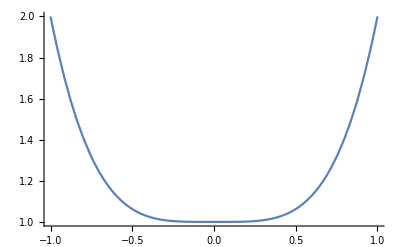

```mathematica
quizz = 1 + x^4
Plot[quizz, {x, -1,1}]
```

```mathematica
P[x_,y_] = ⅇ^(y/x)
Q[x_,y_] = ⅇ^y Log[x]+2 x
```

ⅇ^(y/x)

2 x+ⅇ^y Log[x]

```mathematica
Reduce[1+x^4≤ 2, x]
```

-1≤x≤1

```mathematica
-1≤x≤1
```

-1≤x≤1

```mathematica
D[P[x,y],x]
D[P[x,y],y]
D[Q[x,y],x]
D[Q[x,y],y]
```

-(ⅇ^(y/x) y)/x^2

ⅇ^(y/x)/x

2+ⅇ^y/x

ⅇ^y Log[x]

For the first three of the above, x must not be zero in order for the expressions to be continuous inside the path. Outside of that, continuity does not seem to be an issue.

```mathematica
N[16/5]
```

3.2

```mathematica
stet=∫_-1^-0.001 ∫_(1+x^4)^1 (D[Q[x,y],x]-D[P[x,y],y])ⅆyⅆx
```

∫_-1^-0.001 (ⅇ^(1/x) (-1+ⅇ^(x^3))-(ⅇ (-1+ⅇ^(x^4)))/x-2 x^4)ⅆx

```mathematica
stetN2 = N[∫_-1.293196^-0.001 ∫_(1+x^4)^1 (D[Q[x,y],x]-D[P[x,y],y])ⅆyⅆx]
```

3.20008

There is a problem with finding the limits of integration for x. The y limits are not a problem. But x cannot be zero, though it can be anything above zero. Trying a few limit values, it seems possible to get close to the answer (yellows).

13 - 17 Integral of the normal derivative
Using (9), p. 437, find the value of ∫(∂w)/(∂n)ⅆs taken counterclockwise over the boundary C of the region R.

13.  w = Cosh[x], R the triangle with vertices {0, 0}, {4, 2}, {0, 2}

```mathematica
Clear["Global`*"]
```

This problem is included in the s.m., p. 181. There it is represented that transforming the normal derivative of a Laplacian of the cited function into a double integral is what needs to be done.

```mathematica
Laplacian[Cosh[x],{x}]
```

Cosh[x]

```mathematica
mypoints={{0,0}, {4,2}, {0,2}}
```

{{0,0},{4,2},{0,2}}

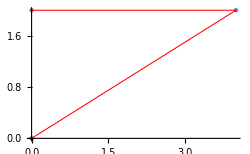

```mathematica
a =ListPlot[mypoints, ImageSize -> 250];
b = ListLinePlot[mypoints, PlotStyle->{Red, Thickness[0.003]}];
Show[a, b]
```

By inspection it is seen that, for the hypotheneuse, y=x/2, or x = 2 y. So the s.m. says that what is
needed is a double integral with x going from 0 to 2 y and y going from 0 to 2.

```mathematica
blaso = ∫_0^2 ∫_0^(2 y) Cosh[x]ⅆxⅆy
```

1/2 (-1+Cosh[4])

The above answer agrees with the text’s.

15.  w=ⅇ^x Cos[y]+x y^3, R: 1≤y≤10-x^2, x≥0

```mathematica
Clear["Global`*"]
```

```mathematica
here = Laplacian[ⅇ^x Cos[y]+x y^3,{x,y}]
```

6 x y

The above agrees with the text’s calculation of the Laplacian.

```mathematica
Reduce[1≤y≤ 10-x^2&&x≥0]
```

(0≤x<3&&1≤y≤10-x^2)||(x==3&&y==1)

{{0,10},{0,1},{3,1}}

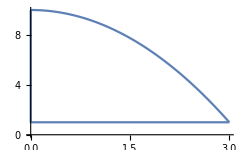

```mathematica
p1 = Plot[10-x^2, {x,0,3}];
plist ={{0,10},{0,1},{3,1}}
p2 =ListLinePlot[plist];
Show[p1,p2]
```

Above is the path. Now to write an integral with limits that walk around it ccw.

```mathematica
blastiddo = ∫_0^3 ∫_1^(10-x^2) 6 x yⅆyⅆx
```

486

The above answer matches the text’s. It seemed appropriate to make ⅆy the inner integral.

17.  w=x^3-y^3, 0≤y≤x^2, |x|≤2

```mathematica
Clear["Global`*"]
```

```mathematica
Lap = Laplacian[x^3-y^3,{x,y}]
```

6 x-6 y

The above agrees with the text’s calculation of the Laplacian.

{{0,0},{2,0},{2,4}}

{{-2,4},{-2,0},{0,0}}

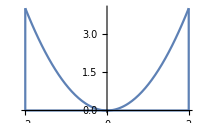

```mathematica
p1 = Plot[x^2, {x,-2,2}, ImageSize ->200];
plist ={{0,0},{2,0},{2,4}}
p2 =ListLinePlot[plist, ImageSize ->200];
p2list ={{-2,4},{-2,0},{0,0}}
p3 =ListLinePlot[p2list, ImageSize ->200];
Show[p1, p2, p3]
```

Above is the path. Now to write an integral with appropriate limits of integration.

```mathematica
blastiddo = ∫_-2^2 ∫_0^(x^2) (6 x -6y)ⅆyⅆx
```

-192/5

```mathematica
-192./5
```

-38.4

The above answer agrees with the text’s. Again I elected to put ⅆy on the inside.

19. Show that w=ⅇ^x Sin[y] satisfies Laplace’s equation ∇w = 0 and, using numbered line (12), p. 438, integrate w(ⅆw/ⅆn) counterclockwise around the boundary curve C of the rectangle 0≤x≤2, 0≤y≤5

```mathematica
Clear["Global`*"]
```

```mathematica
eq[x_,y_] = ⅇ^x Sin[y]
```

ⅇ^x Sin[y]

```mathematica
Lap = Laplacian[ⅇ^x Sin[y],{x,y}]
```

0

```mathematica
ppoints ={{0,0},{2,0},{2,5},{0,5}, {0.001,0}}
```

{{0,0},{2,0},{2,5},{0,5},{0.001,0}}

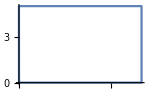

```mathematica
ListLinePlot[ppoints, ImageSize ->150]
```

The problem instructions refer to numbered line (12), an equation contained in the problems, and shown below.

(12)  ∫_R ∫(ⅆw/ⅆx)^2+(ⅆw/ⅆy)^2 ⅆxⅆy=∮_C w ⅆw/ⅆn ⅆs

The partial derivatives in the top line, for the present problem, are the raps:

```mathematica
rap1=D[ⅇ^x Sin[y],x]
```

ⅇ^x Sin[y]

```mathematica
rap2 =D[ⅇ^x Sin[y],y]
```

ⅇ^x Cos[y]

```mathematica
sq=rap1^2+rap2^2
```

ⅇ^(2 x) Cos[y]^2+ⅇ^(2 x) Sin[y]^2

```mathematica
sq1 = TrigReduce[sq]
```

ⅇ^(2 x)

And the top line filled in and executed:

```mathematica
outsq=∫_0^5 ∫_0^2 (sq1)ⅆxⅆy
```

5/2 (-1+ⅇ^4)

The line above agrees with the text’s answer.